# double pendulum

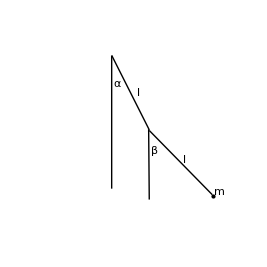

```mathematica
x=l Sin[α[t]]+l Sin[β[t]];
y=-l Cos[α[t]]-l Cos[β[t]];
```

```mathematica
L=1/2 m (D[x,t]^2+D[y,t]^2)-m g y//Simplify
```

1/2 l m (2 g (Cos[α[t]]+Cos[β[t]])+l α'[t]^2+2 l Cos[α[t]-β[t]] α'[t] β'[t]+l β'[t]^2)

```mathematica
D[D[L,α'[t]],t]==D[L,α[t]]//Simplify
D[D[L,β'[t]],t]==D[L,β[t]]//Simplify
```

l m (g Sin[α[t]]+l Sin[α[t]-β[t]] β'[t]^2+l α''[t]+l Cos[α[t]-β[t]] β''[t])==0

l m (g Sin[β[t]]-l Sin[α[t]-β[t]] α'[t]^2+l Cos[α[t]-β[t]] α''[t]+l β''[t])==0

```mathematica
(* Try x = α + β , y = α - β *)
g Sin[α[t]]+l Sin[α[t]-β[t]] β'[t]^2+l α''[t]+l Cos[α[t]-β[t]] β''[t]==0/.{α[t]-> (x+y)/2,β[t]-> (x-y)/2,β'[t]-> (vx-vy)/2,α''[t]-> (ax+ay)/2,β''[t]-> (ax-ay)/2,g->ω^2,l->1}//Simplify
g Sin[β[t]]-l Sin[α[t]-β[t]] α'[t]^2+l Cos[α[t]-β[t]] α''[t]+l β''[t]==0/.{α[t]-> (x+y)/2,β[t]-> (x-y)/2,α'[t]-> (vx+vy)/2,α''[t]-> (ax+ay)/2,β''[t]-> (ax-ay)/2,g->ω^2,l->1}//Simplify
```

2 (ax-ay) Cos[y]+(vx-vy)^2 Sin[y]+2 (ax+ay+2 ω^2 Sin[(x+y)/2])==0

2 (ax+(ax+ay) Cos[y]+2 ω^2 Sin[(x-y)/2])==2 ay+(vx+vy)^2 Sin[y]

```mathematica
(* Adding and Substract *)
2 (ax+(ax+ay) Cos[y]+2 ω^2 Sin[(x-y)/2])+2 (ax-ay) Cos[y]+(vx-vy)^2 Sin[y]+2 (ax+ay+2 ω^2 Sin[(x+y)/2])-2 ay+(vx+vy)^2 Sin[y]//Simplify
2 (ax+(ax+ay) Cos[y]+2 ω^2 Sin[(x-y)/2])-2 (ax-ay) Cos[y]+(vx-vy)^2 Sin[y]-2 (ax+ay+2 ω^2 Sin[(x+y)/2])-2 ay+(vx+vy)^2 Sin[y]//Simplify
```

4 Cos[y/2] (2 ax Cos[y/2]+2 ω^2 Sin[x/2]+(vx^2+vy^2) Sin[y/2])

-4 Sin[y/2] (2 ω^2 Cos[x/2]-(vx^2+vy^2) Cos[y/2]+2 ay Sin[y/2])

```mathematica
ax+ax Cos[y]-vx vy Sin[y]+2 ω^2 Cos[y/2] Sin[x/2]==0
ay-ay Cos[y]+vx vy Sin[y]+2 ω^2 Cos[x/2] Sin[y/2]==0
```

```mathematica
(* Try another α = (x + ⅈ y)/2, β = (x-ⅈ y)/2 *)
g Sin[α[t]]+l Sin[α[t]-β[t]] β'[t]^2+l α''[t]+l Cos[α[t]-β[t]] β''[t]==0/.{α[t]-> (x+ⅈ y)/2,β[t]-> (x-ⅈ y)/2,β'[t]-> (vx-ⅈ vy)/2,α''[t]-> (ax+ⅈ ay)/2,β''[t]-> (ax- ⅈ ay)/2,g->ω^2,l->1}//Simplify
g Sin[β[t]]-l Sin[α[t]-β[t]] α'[t]^2+l Cos[α[t]-β[t]] α''[t]+l β''[t]==0/.{α[t]-> (x+ⅈ y)/2,β[t]-> (x-ⅈ y)/2,α'[t]-> (vx+ⅈ vy)/2,α''[t]-> (ax+ⅈ ay)/2,β''[t]-> (ax-ⅈ ay)/2,g->ω^2,l->1}//Simplify
```

2 (ax-ⅈ ay) Cosh[y]+2 (ax+ⅈ ay+2 ω^2 Sin[1/2 (x+ⅈ y)])+ⅈ (vx-ⅈ vy)^2 Sinh[y]==0

2 (ax+ⅈ ay) Cosh[y]+2 (ax-ⅈ ay+2 ω^2 Sin[1/2 (x-ⅈ y)])-ⅈ (vx+ⅈ vy)^2 Sinh[y]==0

```mathematica
2 (ax-ⅈ ay) Cosh[y]+2 (ax+ⅈ ay+2 ω^2 Sin[1/2 (x+ⅈ y)])+ⅈ (vx-ⅈ vy)^2 Sinh[y]+(2 (ax+ⅈ ay) Cosh[y]+2 (ax-ⅈ ay+2 ω^2 Sin[1/2 (x-ⅈ y)])-ⅈ (vx+ⅈ vy)^2 Sinh[y])==0//Simplify
2 (ax-ⅈ ay) Cosh[y]+2 (ax+ⅈ ay+2 ω^2 Sin[1/2 (x+ⅈ y)])+ⅈ (vx-ⅈ vy)^2 Sinh[y]-(2 (ax+ⅈ ay) Cosh[y]+2 (ax-ⅈ ay+2 ω^2 Sin[1/2 (x-ⅈ y)])-ⅈ (vx+ⅈ vy)^2 Sinh[y])==0//Simplify
```

Cosh[y/2] (ax Cosh[y/2]+ω^2 Sin[x/2]+vx vy Sinh[y/2])==0

Sinh[y/2] (-2 ω^2 Cos[x/2]+(-vx^2+vy^2) Cosh[y/2]+2 ay Sinh[y/2])==0